# QNMspectral examples

Loading the package

```mathematica
Needs["QNMspectral`"]
```

## Getting started

To find out how this package works, apart from going through this notebook one can go to Help -> Documentation and type in “QNMspectral”, to find an introduction and several tutorials.
Also one can get information about its functions just as you would for Mathematica functions, e.g.:

```mathematica
?GetModes
```

GetModes[
StyleBox["equation",
FontSlant->"Italic"],{
StyleBox["N",
FontSlant->"Italic"]
StyleBox[",",
FontSlant->"Italic"]
StyleBox["prec",
FontSlant->"Italic"]}] computes the quasinormal mode spectrum of 
StyleBox["equation",
FontSlant->"Italic"] using a spectral grid of 
StyleBox["N",
FontSlant->"Italic"]+1 points with 
StyleBox["prec",
FontSlant->"Italic"] digits of precision.

Reproducing the AdS_5 QNM’s of Kovtun, Starinets 0506184

## The equations in EF coordinates

These are the equations of the 5 different modes of the AdS_5-Schwarzschild black brane considered in 0506184 (the modes of the metric, and of an external massless vector field).
The coordinates are such that z=0 is the boundary and z=1 is the horizon. 
For ease of comparison λ=ω/(2π T) and k=q/(2π T).
All equations and functions are rescaled so that the function goes linearly to 0 towards the boundary and the equation itself goes to a nontrivial constant (proportional to the function).

```mathematica
hscalar=(3 (3+4 k^2 z^2+9 z^4)-18 ⅈ z λ) Z3[z]+(3 z (-3+7 z^4)-12 ⅈ z^2 λ) Z3'[z]+3 z^2 (-1+z^4) Z3''[z];
hshear=(12 k^2 (3+4 k^2 z^2-3 z^4) (-1+z^4)+24 ⅈ k^2 z (3+z^4) λ+12 (3+4 k^2 z^2+9 z^4) λ^2-72 ⅈ z λ^3) Z1x[z]+(36 k^2 z (-1+z^4)^2-48 ⅈ k^2 z^2 (-1+z^4) λ+12 z (-3+7 z^4) λ^2-48 ⅈ z^2 λ^3) Z1x'[z]+(12 k^2 z^2 (-1+z^4)^2+12 z^2 (-1+z^4) λ^2) Z1x''[z];
hsound=(4 k^2 (-3+z^4) (3+4 k^2 z^2+z^4)+8 ⅈ k^2 z (9+5 z^4) λ+12 (3+4 k^2 z^2+9 z^4) λ^2-72 ⅈ z λ^3) Z2[z]+(-4 k^2 z (-9+16 z^4+z^8)-16 ⅈ k^2 z^2 (-3+z^4) λ+12 z (-3+7 z^4) λ^2-48 ⅈ z^2 λ^3) Z2'[z]+(4 k^2 z^2 (3-4 z^4+z^8)+12 z^2 (-1+z^4) λ^2) Z2''[z];

Atransverse=(1+4 k^2 z^2+3 z^4-2 ⅈ z λ) Ex[z]+(z (-1+5 z^4)-4 ⅈ z^2 λ) Ex'[z]+z^2 (-1+z^4) Ex''[z];
Adiffusive=(4 k^2 (1+4 k^2 z^2-z^4) (-1+z^4)+8 ⅈ k^2 z (1+3 z^4) λ+4 (1+4 k^2 z^2+3 z^4) λ^2-8 ⅈ z λ^3) Ez[z]+(4 k^2 z (-1+z^4)^2-16 ⅈ k^2 z^2 (-1+z^4) λ+4 z (-1+5 z^4) λ^2-16 ⅈ z^2 λ^3) Ez'[z]+(4 k^2 z^2 (-1+z^4)^2+4 z^2 (-1+z^4) λ^2) Ez''[z];
```

## Computing modes at k=1 in all channels

### Scalar channel

#### First at machine precision, using 40 and 60 gridpoints and taking only the converged values

{0.035303,Null}

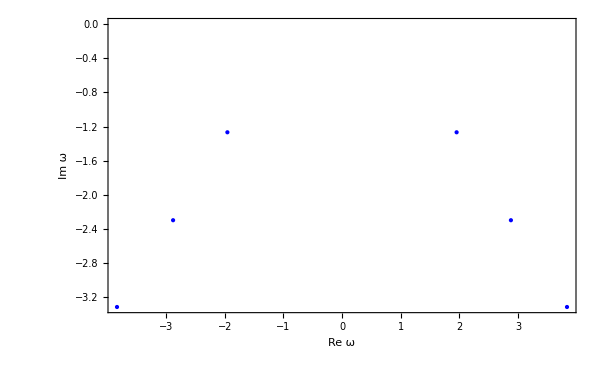
{-Graphics-,n | Re ω_n | Im ω_n
1 | ± 1.954330884 | -1.26732726
2 | ± 2.880263 | -2.29796
3 | ± 3.84 | -3.3}

```mathematica
scalarModes=GetAccurateModes[hscalar/.k->1,{40,0},{60,0}];//AbsoluteTiming
ShowModes[scalarModes]
```

#### Now increase the gridsize and use higher precision (half of the gridsize as by default)

{20.6302,Null}

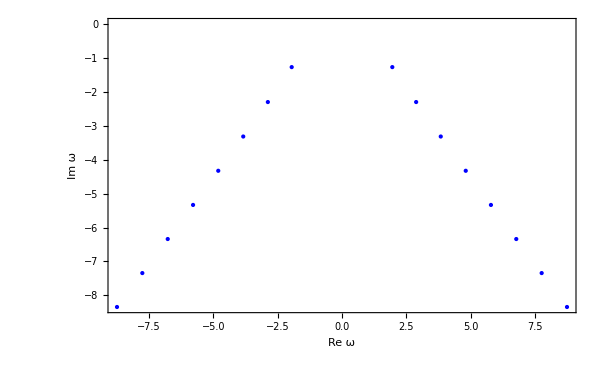
{-Graphics-,n | Re ω_n | Im ω_n
1 | ± 1.954330884 | -1.267327263
2 | ± 2.880262565 | -2.297957047
3 | ± 3.836632223 | -3.31490716
4 | ± 4.807392343 | -4.32587137
5 | ± 5.786181877 | -5.333622204
6 | ± 6.76995787 | -6.3394302
7 | ± 7.75707 | -7.344
8 | ± 8.74 | -8.3}

```mathematica
scalarModesAccurate=GetAccurateModes[hscalar/.k->1,{80},{60}];//AbsoluteTiming
ShowModes[scalarModesAccurate]
```

### Transverse channel

#### First at machine precision, using 40 and 60 gridpoints and taking only the converged values

{0.021124,Null}

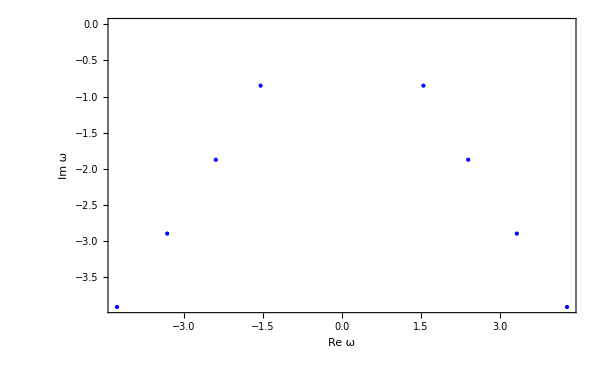
{-Graphics-,n | Re ω_n | Im ω_n
1 | ± 1.547186978 | -0.849723168
2 | ± 2.3989034 | -1.874343
3 | ± 3.3232 | -2.895
4 | ± 4.3 | -4.}

```mathematica
AtransverseModes=GetAccurateModes[Atransverse/.k->1,{40,0},{60,0}];//AbsoluteTiming
ShowModes[AtransverseModes]
```

#### Now increase the gridsize and use higher precision (half of the gridsize as by default)

{17.6608,Null}

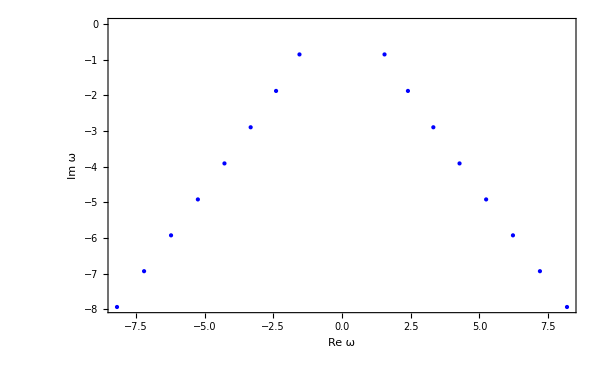
{-Graphics-,n | Re ω_n | Im ω_n
1 | ± 1.547186978 | -0.8497231684
2 | ± 2.398903399 | -1.87434316
3 | ± 3.323228898 | -2.894900786
4 | ± 4.276431262 | -3.90958318
5 | ± 5.244058297 | -4.920346429
6 | ± 6.220036274 | -5.928545741
7 | ± 7.201341 | -6.935
8 | ± 8.186 | -7.94}

```mathematica
AtransverseModesAccurate=GetAccurateModes[Atransverse/.k->1,{80},{60}];//AbsoluteTiming
ShowModes[AtransverseModesAccurate]
```

### Shear channel

For this equation, notice first that it contains a third power of λ. We have to linearize the equations in λ by defining new functions which are λ-multiples of the original. 
This is done automatically, but it results in a matrix which is of size 3x the grid size. 
Of course this slows down the computation, alternatively one can sweep the complex plane looking for zeroes of the determinant.

Note that near the boundary the equation is proportional to λ^2-k^2:

```mathematica
Series[hshear,{z,0,0}]//Simplify
```

36 (-k^2+λ^2) Z1x[0]+O[z]^1

This causes the appearance of incorrect solutions where λ≈±k, which unfortunately are not filtered out by ‘GetAccurateModes’.

#### First at machine precision, using 40 and 60 gridpoints and taking only the converged values

{0.202068,Null}

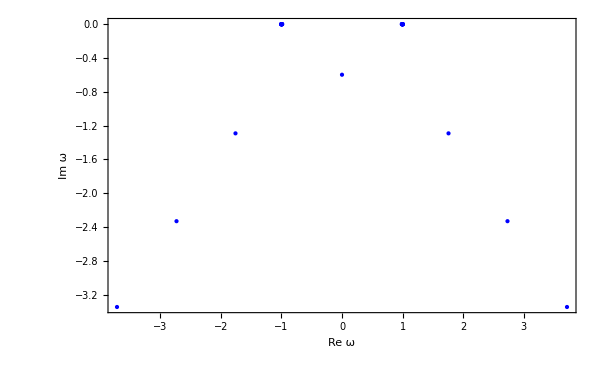
{-Graphics-,n | Re ω_n | Im ω_n
1 | ± 1. | 0.
2 | 0. | -0.598065737
3 | ± 1.759115585 | -1.2915938
4 | ± 2.733081 | -2.3304
5 | ± 3.716 | -3.35}

```mathematica
shearModes=GetAccurateModes[hshear/.k->1,{40,0},{60,0}];//AbsoluteTiming
ShowModes[shearModes]
```

#### Now increase the gridsize and use higher precision (half of the gridsize as by default)

{249.424,Null}

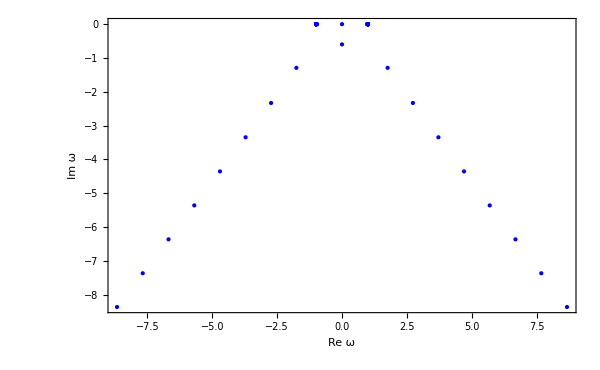
{-Graphics-,n | Re ω_n | Im ω_n
1 | ± 1. | 0.
2 | 0. | -0.598065737
3 | ± 1.759115585 | -1.291593797
4 | ± 2.733081271 | -2.330404854
5 | ± 3.715933163 | -3.345342808
6 | ± 4.703643573 | -4.353493464
7 | ± 5.694378384 | -5.358729265
8 | ± 6.68711564 | -6.3624227
9 | ± 7.68125 | -7.3652
10 | ± 8.67 | -8.4}

```mathematica
shearModesAccurate=GetAccurateModes[hshear/.k->1,{80},{60}];//AbsoluteTiming
ShowModes[shearModesAccurate,PlotRange->All]
```

#### Filter eigenfunctions

Note that there are still a lot of unphysical eigenvalues, those with imaginary part equal or close to zero.
To filter these out, we can check if the corresponding eigenfunctions are finite, smooth and nonzero.
To do this we must of course compute them. Instead of setting Eigenfunctions -> True, we use Eigenfunctions -> “Later” here. This will first compute the eigenvalues without the eigenfunctions, then check which have converged, and only for those compute the corresponding eigenfunction. This is not always faster, but in this case it is.
Finally we also do a more strict test on convergence by setting Cutoff -> 6, demanding 6 digits of agreement between the two computations

{0.533244,Null}

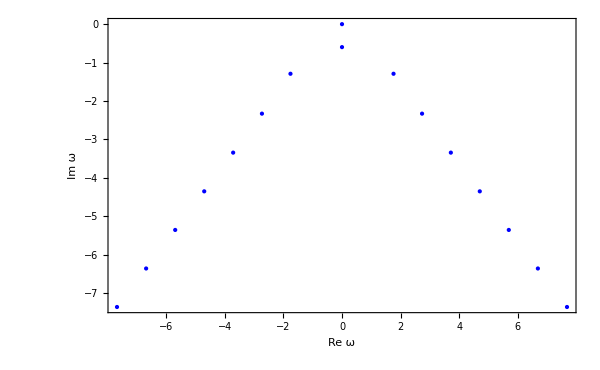
{-Graphics-,n | Re ω_n | Im ω_n
1 | 0 | 0
2 | 0. | -0.598065737
3 | ± 1.759115585 | -1.291593797
4 | ± 2.733081271 | -2.330404854
5 | ± 3.715933163 | -3.345342808
6 | ± 4.703643573 | -4.353493464
7 | ± 5.694378384 | -5.358729265
8 | ± 6.68711564 | -6.3624227
9 | ± 7.68125 | -7.3652}

```mathematica
shearModesAccurate2=GetAccurateModes[hshear/.k->1,{80},{60},Eigenfunctions->"Later",Cutoff->6,FilterEigenfunctions->True];//AbsoluteTiming
ShowModes[shearModesAccurate2,PlotRange->All]
```

Note that in this case the computation is much faster because we could use the already computed eigenvalues.

#### filter modes

Unfortunately there is still one unphysical mode left, with frequency exactly zero.
We can see why this is there by inspecting our equation at zero frequency:

```mathematica
hshear/.k->1/.λ->0//Simplify
```

12 (-1+z^4) ((3+4 z^2-3 z^4) Z1x[z]+z (-1+z^4) (3 Z1x'[z]+z Z1x''[z]))

We see that (1-z^4) factors out, this is trivially satisfied at the horizon. If we actually take out this factor and solve at the horizon we find that Z1x has to vanish there:

```mathematica
(hshear/(-1+z^4)/.k->1/.λ->0//Simplify)/.z->1
```

48 Z1x[1]

We can also plug it back into the equation and see explicitly that it isn’t solved:

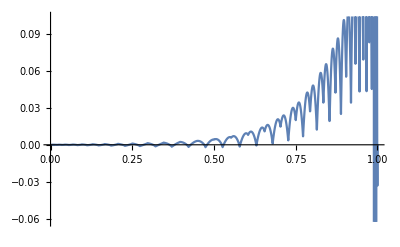

```mathematica
zeromodeSol=Interpolation@Transpose[{MakeGrid[60],shearModesAccurate2⟦1,2,1⟧//Re}];
Plot[hshear/.k->1/.λ->0/.Z1x->zeromodeSol,{z,0,1}]
```

We stress that one can never guarantee that these filters filter out all the unphysical modes and none of the physical ones, one has to be careful with these and check on a case by case basis.

### Diffusive channel

Similar to the shear channel, there are incorrect solutions here at λ≈±k, and an incorrect zero mode, for the same reason.

#### First at machine precision, using 40 and 60 gridpoints and taking only the converged values

{0.144022,Null}

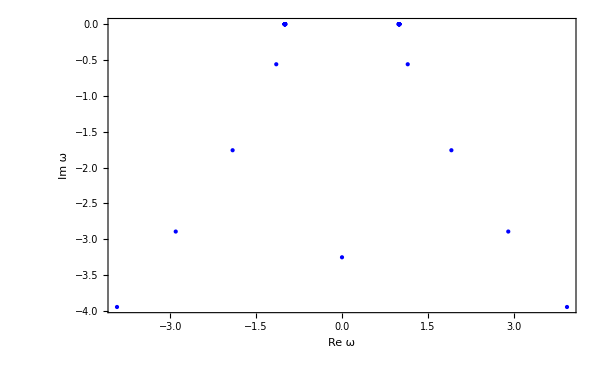
{-Graphics-,n | Re ω_n | Im ω_n
1 | ± 1. | 0.
2 | ± 1.147831436 | -0.5592035651
3 | ± 1.9100059 | -1.758065
4 | ± 2.9033 | -2.892
5 | 0. | -3.2506
6 | ± 4. | -3.9}

```mathematica
AdiffusiveModes=GetAccurateModes[Adiffusive/.k->1,{40,0},{60,0}];//AbsoluteTiming
ShowModes[AdiffusiveModes,PlotRange->All]
```

#### Now increase the gridsize and use higher precision, and filters

{241.129,Null}

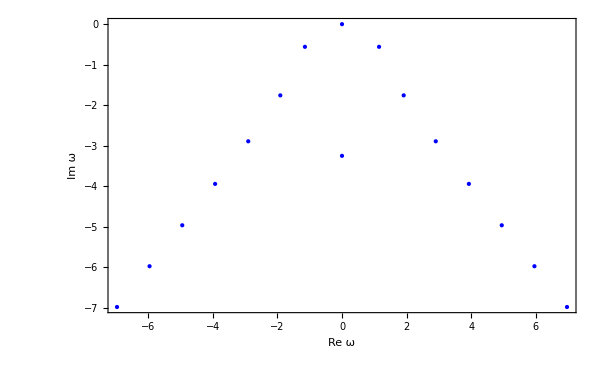
{-Graphics-,n | Re ω_n | Im ω_n
1 | 0 | 0
2 | ± 1.147831436 | -0.5592035651
3 | ± 1.910005925 | -1.758064794
4 | ± 2.903293081 | -2.891680855
5 | 0. | -3.250637029
6 | ± 3.928555317 | -3.943385929
7 | ± 4.946818212 | -4.965185141
8 | ± 5.958793511 | -5.976169494
9 | ± 6.96692 | -6.982483}

```mathematica
AdiffusiveModesAccurate=GetAccurateModes[Adiffusive/.k->1,{80},{60},Eigenfunctions->"Later",Cutoff->6,FilterEigenfunctions->True];//AbsoluteTiming
ShowModes[AdiffusiveModesAccurate,PlotRange->All]
```

By comparing with the time it took to compute the shear channel without computing the eigenfunctions, we see that this added computation when computing them only for the converged modes takes very little time, as opposed to calculating them at the start, where it would take roughly twice as long.

### Sound channel

Similar to the shear channel, there are incorrect solutions here at λ≈±k, but no zero mode.

#### First at machine precision, using 40 and 60 gridpoints and taking only the converged values

{0.160439,Null}

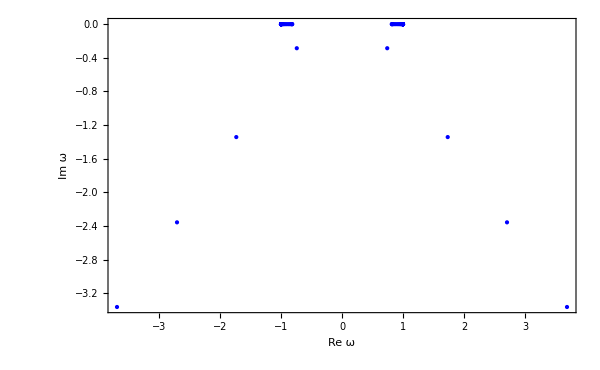
{-Graphics-,n | Re ω_n | Im ω_n
1 | ± 1. | 0.
2 | ± 0.7414299655 | -0.286280007
3 | ± 1.73351109 | -1.3430075
4 | ± 2.70554 | -2.3571
5 | ± 3.69 | -3.4}

```mathematica
soundModes=GetAccurateModes[hsound/.k->1,{40,0},{60,0}];//AbsoluteTiming
ShowModes[soundModes,PlotRange->All]
```

#### Now increase the gridsize and use higher precision, and filters

{245.598,Null}

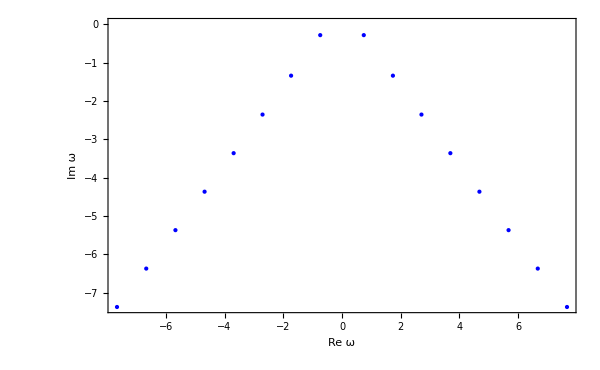
{-Graphics-,n | Re ω_n | Im ω_n
1 | ± 0.7414299655 | -0.2862800072
2 | ± 1.733511095 | -1.343007549
3 | ± 2.705539866 | -2.357061908
4 | ± 3.689391462 | -3.363863379
5 | ± 4.678735426 | -4.367980846
6 | ± 5.671090621 | -5.370783926
7 | ± 6.66529112 | -6.3728353
8 | ± 7.66071 | -7.3744}

```mathematica
soundModesAccurate=GetAccurateModes[hsound/.k->1,{80},{60},Eigenfunctions->"Later",Cutoff->6,FilterEigenfunctions->True];//AbsoluteTiming
ShowModes[soundModesAccurate,PlotRange->All]
```

## Tables

#### The tables found on page 26

```mathematica
MakeTable[#,"Precision"->7]&/@(Select[#,If[NumericQ[#],Abs[Im@#],Abs[Im@#⟦1⟧]]>.1&]&/@{AtransverseModesAccurate,AdiffusiveModesAccurate,scalarModesAccurate,shearModesAccurate2,soundModesAccurate})
```

{n | Re ω_n | Im ω_n
1 | ± 1.547187 | -0.8497232
2 | ± 2.398903 | -1.874343
3 | ± 3.323229 | -2.894901
4 | ± 4.276431 | -3.909583
5 | ± 5.244058 | -4.920346
6 | ± 6.220036 | -5.928546
7 | ± 7.201341 | -6.935
8 | ± 8.186 | -7.94,n | Re ω_n | Im ω_n
1 | ± 1.147831 | -0.5592036
2 | ± 1.910006 | -1.758065
3 | ± 2.903293 | -2.891681
4 | 0. | -3.250637
5 | ± 3.928555 | -3.943386
6 | ± 4.946818 | -4.965185
7 | ± 5.958794 | -5.976169
8 | ± 6.96692 | -6.982483,n | Re ω_n | Im ω_n
1 | ± 1.954331 | -1.267327
2 | ± 2.880263 | -2.297957
3 | ± 3.836632 | -3.314907
4 | ± 4.807392 | -4.325871
5 | ± 5.786182 | -5.333622
6 | ± 6.769958 | -6.33943
7 | ± 7.75707 | -7.344
8 | ± 8.74 | -8.3,n | Re ω_n | Im ω_n
1 | 0. | -0.5980657
2 | ± 1.759116 | -1.291594
3 | ± 2.733081 | -2.330405
4 | ± 3.715933 | -3.345343
5 | ± 4.703644 | -4.353493
6 | ± 5.694378 | -5.358729
7 | ± 6.687116 | -6.362423
8 | ± 7.68125 | -7.3652,n | Re ω_n | Im ω_n
1 | ± 0.74143 | -0.28628
2 | ± 1.733511 | -1.343008
3 | ± 2.70554 | -2.357062
4 | ± 3.689391 | -3.363863
5 | ± 4.678735 | -4.367981
6 | ± 5.671091 | -5.370784
7 | ± 6.665291 | -6.372835
8 | ± 7.66071 | -7.3744}

Note the additional hydrodynamic modes compared to the table on page 26, which they write above the table.
Also note the occasional discrepancy in the last few digits of some higher modes.

## Plots (at low accuracy)

```mathematica
removeIncorrectModes[modes_]:=Select[modes,Abs[Im[#]]>.005&&Re[#]>-0.01&]
ω0Sound[kval_]:=GetAccurateModes[hsound/.k->kval,{50,0},{80,0},"Quiet"->True]//removeIncorrectModes
ω0Scalar[kval_]:=GetAccurateModes[hscalar/.k->kval,{50,0},{80,0},"Quiet"->True]//removeIncorrectModes
ω0Transverse[kval_]:=GetAccurateModes[Atransverse/.k->kval,{50,0},{80,0},"Quiet"->True]//removeIncorrectModes
ω0Diffusive[kval_]:=GetAccurateModes[Adiffusive/.k->kval,{50,0},{80,0},"Quiet"->True]//removeIncorrectModes
ω0Shear[kval_]:=GetAccurateModes[hshear/.k->kval,{50,0},{80,0},"Quiet"->True]//removeIncorrectModes
```

```mathematica
removeIncorrectModes[modes_]:=Select[modes,Abs[Im[#]]>.005&&Re[#]>-0.01&]
ω0Sound[kval_]:=GetAccurateModes[hsound/.k->kval,{50,0},{80,0}]//removeIncorrectModes
ω0Scalar[kval_]:=GetAccurateModes[hscalar/.k->kval,{50,0},{80,0}]//removeIncorrectModes
ω0Transverse[kval_]:=GetAccurateModes[Atransverse/.k->kval,{50,0},{80,0}]//removeIncorrectModes
ω0Diffusive[kval_]:=GetAccurateModes[Adiffusive/.k->kval,{50,0},{80,0}]//removeIncorrectModes
ω0Shear[kval_]:=GetAccurateModes[hshear/.k->kval,{50,0},{80,0}]//removeIncorrectModes
```

### Sound, figure 5

```mathematica
$QNMQuiet=True;
soundlist=Monitor[Table[{k,ω0Sound[k]},{k,.1,5,.1}],k];//AbsoluteTiming
```

{10.1675,Null}

```mathematica
ClearAll[sortModes]
sortModes[modes_,nmodes_ : -1]:=Block[{ωlists=modes/.{k_,ωlist_List}:>({k,#}&/@ωlist⟦1;;Min[nmodes,Length@ωlist]⟧)//Transpose,splitlists},
splitlists=Split[#,Abs[#1⟦2⟧-#2⟦2⟧]<.3&]&/@ωlists//Flatten[#,1]&//DeleteCases[#,list_List /;Length[list]<3]&;
SortBy[First]/@(Flatten[#,1]&/@Gather[splitlists,Min[DistanceMatrix[#1,#2]]<0.25&])
]
```

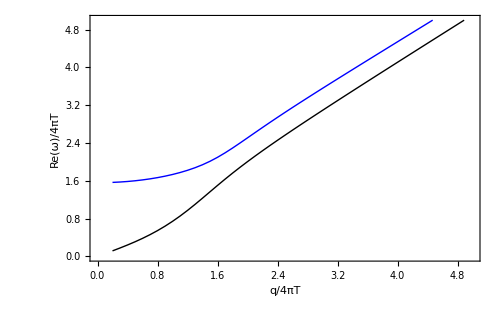
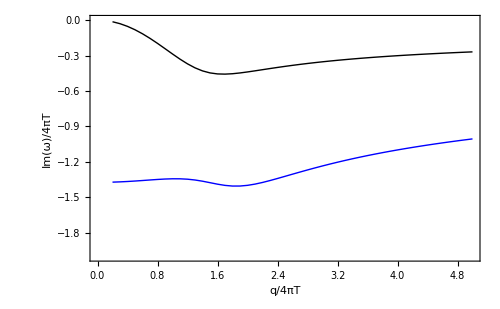

```mathematica
plotopts=Sequence[Frame->True,Joined->True,PlotStyle->{{Black,Thick},{Blue,Thick},{Green,Thick}},ImageSize->500,BaseStyle->20];
{(soundlist//sortModes[#,2]&)/.Complex[a_,b_]:>Abs[a]//ListPlot[#,FrameLabel->{"q/4πT","Re(ω)/4πT"},PlotRange->{{0,5},{0,5}},plotopts]&,
(soundlist//sortModes[#,2]&)/.Complex[a_,b_]:>b//ListPlot[#,FrameLabel->{"q/4πT","Im(ω)/4πT"},PlotRange->{{0,5},{-2,0}},plotopts]&}
```

#### Or in movie form:

```mathematica
Manipulate[soundlist⟦n,2⟧~Join~(soundlist⟦n,2⟧/.Complex[a_,b_]:>Complex[-a,b])//PlotFrequencies[#,PlotRange->{{-7,7},{-5,0}},PlotLabel->"k = "<>ToString[soundlist⟦n,1⟧]]&,{n,1,Length@soundlist,1}]
```

### scalar

```mathematica
scalarlist=Monitor[Table[{k,ω0Scalar[k]},{k,.1,5,.1}],k];//AbsoluteTiming
```

{1.54859,Null}

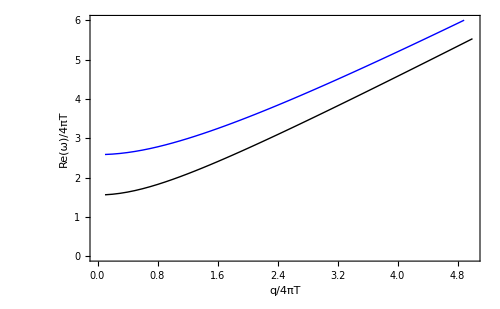
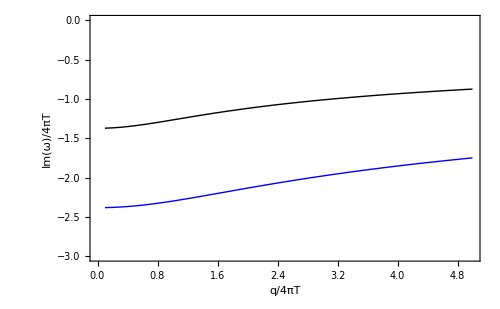

```mathematica
{(scalarlist//sortModes[#,2]&)/.Complex[a_,b_]:>Abs[a]//ListPlot[#,FrameLabel->{"q/4πT","Re(ω)/4πT"},PlotRange->{{0,5},{0,6}},plotopts]&,
(scalarlist//sortModes[#,2]&)/.Complex[a_,b_]:>b//ListPlot[#,FrameLabel->{"q/4πT","Im(ω)/4πT"},PlotRange->{{0,5},{-3,0}},plotopts]&}
```

### transverse

```mathematica
transverselist=Monitor[Table[{k,ω0Transverse[k]},{k,.1,5,.1}],k];//AbsoluteTiming
```

{1.50345,Null}

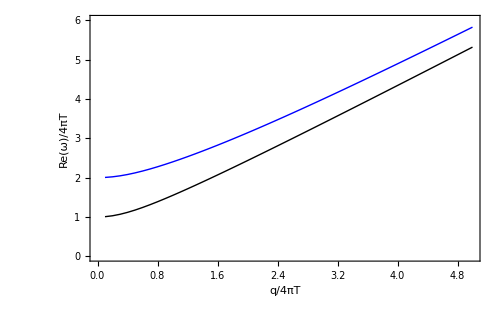
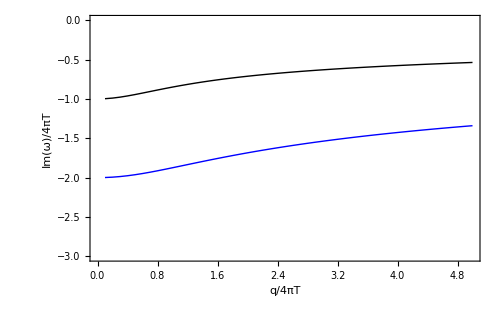

```mathematica
{(transverselist//sortModes[#,2]&)/.Complex[a_,b_]:>Abs[a]//ListPlot[#,FrameLabel->{"q/4πT","Re(ω)/4πT"},PlotRange->{{0,5},{0,6}},plotopts]&,
(transverselist//sortModes[#,2]&)/.Complex[a_,b_]:>b//ListPlot[#,FrameLabel->{"q/4πT","Im(ω)/4πT"},PlotRange->{{0,5},{-3,0}},plotopts]&}
```

### diffusive

```mathematica
diffusivelist=Monitor[Table[{k,ω0Diffusive[k]},{k,.1,5,.1}],k];//AbsoluteTiming
```

{10.5127,Null}

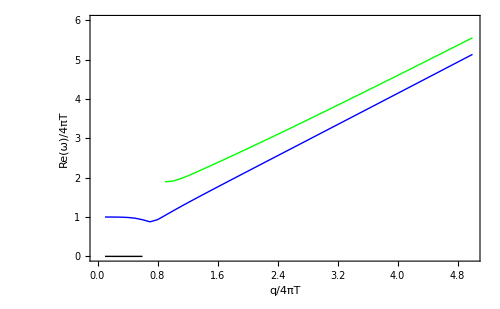
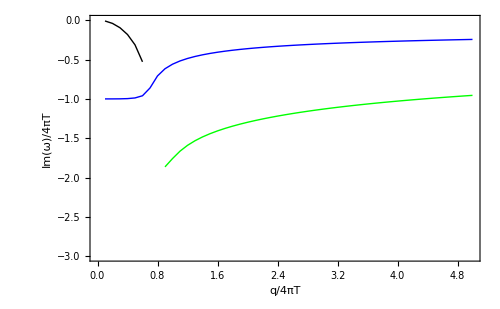

```mathematica
{(diffusivelist//sortModes[#,2]&)/.Complex[a_,b_]:>Abs[a]//ListPlot[#,FrameLabel->{"q/4πT","Re(ω)/4πT"},PlotRange->{{0,5},{0,6}},plotopts]&,
(diffusivelist//sortModes[#,2]&)/.Complex[a_,b_]:>b//ListPlot[#,FrameLabel->{"q/4πT","Im(ω)/4πT"},PlotRange->{{0,5},{-3,0}},plotopts]&}
```

### shear

```mathematica
shearlist=Monitor[Table[{k,ω0Shear[k]},{k,.1,5,.1}],k];//AbsoluteTiming
```

{10.7628,Null}

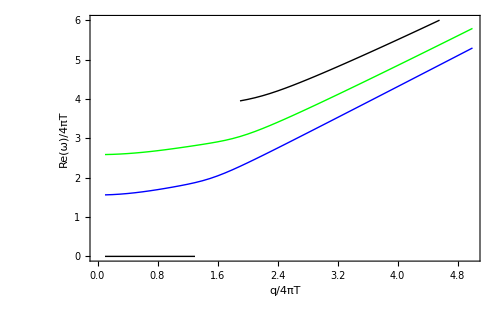
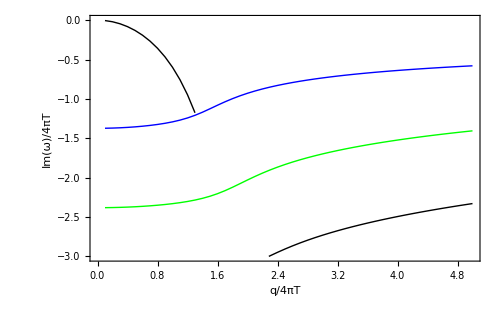

```mathematica
{(shearlist//sortModes[#,3]&)/.Complex[a_,b_]:>Abs[a]//ListPlot[#,FrameLabel->{"q/4πT","Re(ω)/4πT"},PlotRange->{{0,5},{0,6}},plotopts]&,
(shearlist//sortModes[#,3]&)/.Complex[a_,b_]:>b//ListPlot[#,FrameLabel->{"q/4πT","Im(ω)/4πT"},PlotRange->{{0,5},{-3,0}},plotopts]&}
```

Reproducing the massless probe scalar modes in Lifshitz of 1602.01375

The equation for a massless probe scalar in the background of an asymptotically Lifshitz black brane of d+1 bulk dimensions with Lifshitz scaling z. 
The function δϕ is scaled such that it goes linearly to zero near the boundary, and the equation goes to a constant on the boundary (proportional to δϕ).
The frequency is λ=ω/(4 π T).

Note that the QNM’s depend only on the ratio α=z/(d-1), which is not immediately apparent from this form of the equation, but this form turns out to be more convenient numerically than the form where it is apparent.

```mathematica
eqLifshitz=(2-d-z-u^(-1+d+z) (-2+d+z)^2+ⅈ u^z (-1+d+z) (-3+d+2 z) λ) δϕ[u]+(u^(d+z) (3-2 d-2 z)+u (-2+d+z+2 ⅈ u^z (-1+d+z) λ)) δϕ'[u]+(u^2-u^(1+d+z)) δϕ''[u];
```

## Relaxation time

The lowest mode, which determines the relaxation time, can be found quite accurately with low precision.

```mathematica
τ[α_?NumericQ]:=-1/(GetAccurateModes[eqLifshitz/.z->α(d-1)/.d->3,{50,0},{80,0}]//First//Im)
```

```mathematica
taulist=Monitor[Table[{α,τ[α]},{α,1/3,3,1/100}],α//N];//AbsoluteTiming
```

{7.64669,Null}

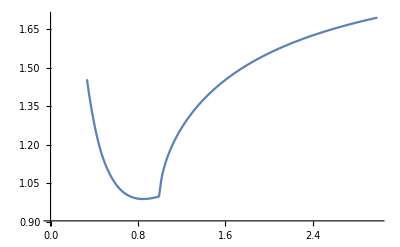

```mathematica
ListPlot[taulist,Joined->True,PlotRange->{.9,1.7}]
```

## Underdamped vs overdamped

For α≥ 1 all modes are overdamped, while for α<1 all are underdamped:

```mathematica
overdamped=GetAccurateModes[eqLifshitz/.z->4/.d->4,{50},{100}];//AbsoluteTiming
```

{22.5071,Null}

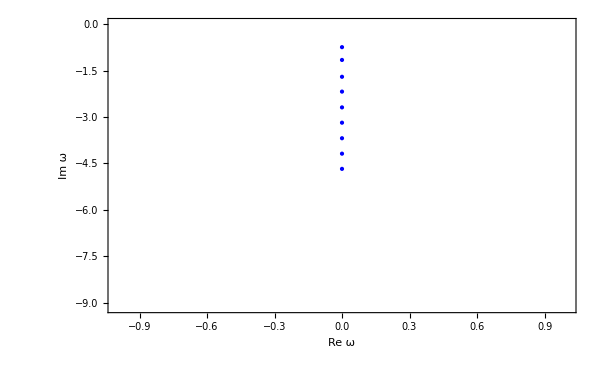
{-Graphics-,n | Re ω_n | Im ω_n
1 | 0. | -0.7438517908
2 | 0. | -1.157079049
3 | 0. | -1.701430076
4 | 0. | -2.18052965
5 | 0. | -2.69086483
6 | 0. | -3.185853
7 | 0. | -3.6883
8 | 0. | -4.19
9 | 0. | -4.7
10 | 0. | -110.}

```mathematica
overdamped//ShowModes
```

```mathematica
underdamped=GetAccurateModes[eqLifshitz/.z->2/.d->4,{50},{100}];//AbsoluteTiming
```

{26.0019,Null}

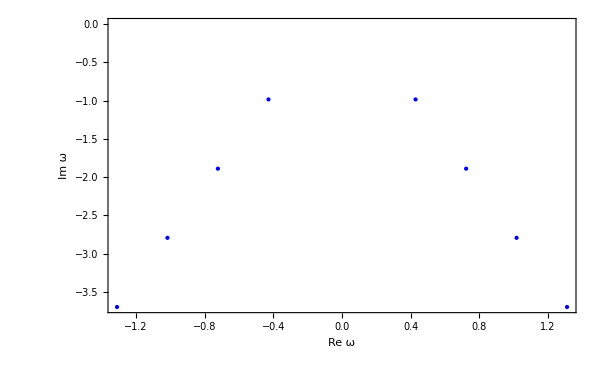
{-Graphics-,n | Re ω_n | Im ω_n
1 | ± 0.4287527555 | -0.9843138988
2 | ± 0.7237153607 | -1.889523443
3 | ± 1.01787 | -2.794092
4 | ± 1.31 | -3.699}

```mathematica
underdamped//ShowModes
```